## Example: Weather simulation (Section 1.7)

### Transition matrix

```mathematica
P:={{0.8,0.2},{0.5,0.5}};
P//MatrixForm
```

(0.8 | 0.2
0.5 | 0.5)

## Simulate weather on days 0,1,...,n, if it was cloudy on day 0.

### Initial distribution: on Monday it’s cloudy

```mathematica
mu0:={{1,0}};
mu0//MatrixForm
```

(1 | 0)

### Wish to pick Tuesday’s weather randomly from transition matrix (“cloudy” row 1)

Matrix element P(1,1) (from cloudy to cloudy):

```mathematica
P11 := Part[P,1,1]; 
P11
```

0.8

Matrix element P(1,2) (from cloudy to sunny):

```mathematica
P12 := Part[P,1,2]; 
P12
```

0.2

Sanity check: row sum equals one!

```mathematica
P11+P12
```

1.

### Construct (pseudo)random variable with probabilities P11 (cloudy) and P12 (sunny)

```mathematica
U := RandomReal[{0,1}];
```

If U < 0.8, the next day is cloudy, otherwise, the next day is sunny.

```mathematica
V=N[U]
If[V<0.8,Print["Tuesday is cloudy"] ,Print["Tuesday is sunny"] ]
```

0.121577

Tuesday is cloudy

```mathematica
V
If[V<0.8,V=N[U]; If[V<0.8,Print["Wednesday is cloudy"] ,Print["Wednesday is sunny"] ],V=N[U];If[V<0.5,Print["Wednesday is cloudy"] ,Print["Wednesday is sunny"] ]]
V
```

0.121577

Wednesday is cloudy

0.26917

## Simulate more days

```mathematica
T=Table[Subscript[w,j-1],{i,1},{j,15}];
T//MatrixForm
```

(w_0 | w_1 | w_2 | w_3 | w_4 | w_5 | w_6 | w_7 | w_8 | w_9 | w_10 | w_11 | w_12 | w_13 | w_14)

```mathematica
T[[1,1]]=1;
T//MatrixForm
```

(1 | w_1 | w_2 | w_3 | w_4 | w_5 | w_6 | w_7 | w_8 | w_9 | w_10 | w_11 | w_12 | w_13 | w_14)

```mathematica
For[n=1,n<15,n++,
V=N[U];If[V<0.8,V=N[U]; If[V<0.8,T[[1,n+1]]=1,T[[1,n+1]]=2 ],V=N[U];If[V<0.5,T[[1,n+1]]=1 ,T[[1,n+1]]=2 ]]];
T//MatrixForm
```

(1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1)

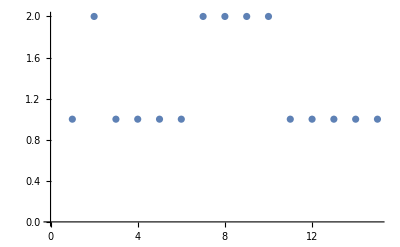

```mathematica
ListPlot[T]
```

### Let’s make a larger example!

```mathematica
T=Table[Subscript[w,j-1],{i,1},{j,100}];
T[[1,1]]=1;
```

```mathematica
For[n=1,n<100,n++,
V=N[U];If[V<0.8,V=N[U]; If[V<0.8,T[[1,n+1]]=1,T[[1,n+1]]=2 ],V=N[U];If[V<0.5,T[[1,n+1]]=1 ,T[[1,n+1]]=2 ]]];
```

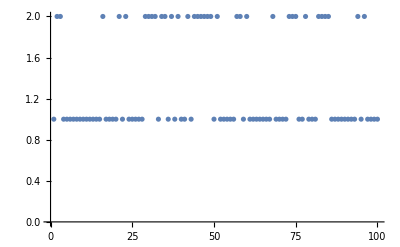

```mathematica
ListPlot[T]
```